# Вольфрам модель температурного поля в грунті

```mathematica
Needs["NDSolve`FEM`"]
```

Запишемо рівняння та фізичні умови

```mathematica
c = 600;
λ = 1;
ρ=1400;
equation = c ρ D[u[t,x],t]-D[λ D[u[t,x],x],x]
```

-u^(0,2)[t,x]+840000 u^(1,0)[t,x]

Задамо меш

ElementMesh[{{0.,10.}},{LineElement[<50>]}]

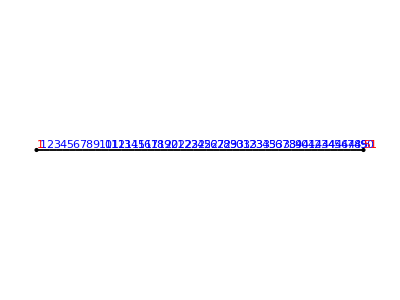

```mathematica
zmax=10;
tmax = 3600 24 2 365;
step = 1/5;
coordinates=Table[{i},{i,0,zmax,step}];
indices = Table[{i,i+1},{i,1,zmax/step}];
mesh = ToElementMesh[
"Coordinates"->coordinates,
"MeshElements"->{LineElement[indices]}]
Show[mesh["Wireframe"] ,
mesh["Wireframe"["MeshElementIDStyle"->Blue]],
mesh["Wireframe"["MeshElement"->"PointElements","MeshElementIDStyle"->Red]]]
```

Задамо граничні умови

```mathematica
γ = 1;
σ = 56704 10^-12;
Tatm = 15+Sin[2Pi t/360];
k=1/2;
Trelict = 2;
Gearth = NeumannValue[-3/100,x==zmax];
Gconv =NeumannValue[ γ(u[t,x]-Tatm[t]),x==0];
Gradiative = NeumannValue[σ k (u[t,x]-Trelict)^4,x==0];
```

Знайдемо розвязок

```mathematica
uif=NDSolveValue[{equation==0,u[0,x]==0,u[t,zmax]==7,DirichletCondition[u[t,x]==12Sin[(2Pi t)/(24 3600 365)],x==0]},u,{t,0,tmax},{x}∈mesh]
```

7
InterpolatingFunction[{{0., 6.3072 10 }, {0., 10.}}, <>]

Виводимо дані

```mathematica
Manipulate[Plot[uif[t,x],{x,0,zmax},PlotRange->{-10,10},AspectRatio->1/3],{t,0,tmax}]
ContourPlot[uif[t,x],{t,0,tmax},{x,0,zmax},ColorFunction->"TemperatureMap",Contours->Function[{min,max},Range[min,max,0.2]],AspectRatio->1/3]
```

-Graphics-

# Обробка даних із Cімулінк моделі

Імпорт даних

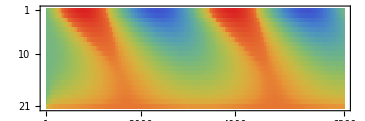

```mathematica
filename = "GroundTempData";
MeshNum = 20;
Time=Flatten[Import[NotebookDirectory[]<>filename<>"Time"<>".csv"]];
data=Transpose@Import[NotebookDirectory[]<>filename<>"Signals.csv"];
CoordData = Map[Transpose[{Table[i/MeshNum 10,{i,0,MeshNum,1}],#}]&,Transpose@data];
MatrixPlot[data-1,AspectRatio->1/3,ColorFunction->"Rainbow"]
```

# Порівняння даних з сімулінк і математики

```mathematica
Manipulate[Show[Plot[uif[t, x],{x,0,10},ColorFunction->Function[{x,y},Red],PlotRange->{-12,12}],ListPlot[CoordData[[Round[t(Dimensions[CoordData][[1]]-1)/tmax]+1,All]],Joined->True,PlotRange->{-12,12}]],{t,0,tmax}]
```

```mathematica
anim = Table[Show[Plot[uif[t, x],{x,0,10},ColorFunction->Function[{x,y},Red],PlotRange->{-12,12}],ListPlot[CoordData[[Round[t(Dimensions[CoordData][[1]]-1)/tmax]+1,All]],Joined->True,PlotRange->{-12,12}]],{t,0,tmax,tmax/20}];
```

```mathematica
Export[NotebookDirectory[]<>"\\omg.gif",anim]
```

C:\Users\Oleg\Drive\Documents_Files\Projects\GroundTemperature\\omg.gif